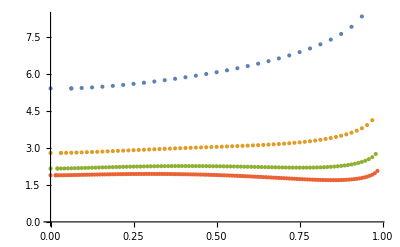

```mathematica
a={{0,5.404137},{0.062500,5.405383},{0.062500,5.405383},{0.093750,5.421956},{0.125000,5.445248},{0.156250,5.474318},{0.187500,5.508337},{0.218750,5.546740},{0.250000,5.589143},{0.281250,5.635300},{0.312500,5.685068},{0.343750,5.738391},{0.375000,5.795289},{0.406250,5.855854},{0.437500,5.920246},{0.468750,5.988696},{0.500000,6.061509},{0.531250,6.139073},{0.562500,6.221867},{0.593750,6.310485},{0.625000,6.405654},{0.656250,6.508282},{0.687500,6.619513},{0.718750,6.740824},{0.750000,6.874191},{0.781250,7.022362},{0.812500,7.189386},{0.843750,7.381690},{0.875000,7.610636},{0.906250,7.900093},{0.937500,8.318570}};
c={{0,11.166299},{0.062500,11.166816},{0.062500,11.166816},{0.093750,11.181740},{0.125000,11.202293},{0.156250,11.227329},{0.187500,11.255812},{0.218750,11.286966},{0.250000,11.320190},{0.281250,11.355004},{0.312500,11.391014},{0.343750,11.427894},{0.375000,11.465367},{0.406250,11.503199},{0.437500,11.541189},{0.468750,11.579165},{0.500000,11.616982},{0.531250,11.654515},{0.562500,11.691662},{0.593750,11.728339},{0.625000,11.764480},{0.656250,11.800037},{0.687500,11.834978},{0.718750,11.869288},{0.750000,11.902967},{0.781250,11.936032},{0.812500,11.968517},{0.843750,12.000472},{0.875000,12.031967},{0.906250,12.063087},{0.937500,12.093939},{0.968750,12.124648},{1.000000,12.155363},{1.031250,12.186255},{1.062500,12.217519},{1.093750,12.249378},{1.125000,12.282082},{1.156250,12.315915},{1.187500,12.351193},{1.218750,12.388269},{1.250000,12.427538},{1.281250,12.469437},{1.312500,12.514456},{1.343750,12.563137},{1.375000,12.616084},{1.406250,12.673970},{1.437500,12.737548},{1.468750,12.807662},{1.500000,12.885264},{1.531250,12.971435},{1.562500,13.067413},{1.593750,13.174636},{1.625000,13.294799},{1.656250,13.429935},{1.687500,13.582551},{1.718750,13.755822},{1.750000,13.953931},{1.781250,14.182639},{1.812500,14.450361},{1.843750,14.770361},{1.875000,15.165924},{1.906250,15.685575},{1.937500,16.467065}};
b=c*Table[{0.5,0.25},{i,0,62}];
f={{0,19.454136},{0.062500,19.454610},{0.062500,19.454610},{0.093750,19.469435},{0.125000,19.489823},{0.156250,19.514613},{0.187500,19.542757},{0.218750,19.573463},{0.250000,19.606117},{0.281250,19.640220},{0.312500,19.675361},{0.343750,19.711195},{0.375000,19.747424},{0.406250,19.783788},{0.437500,19.820059},{0.468750,19.856037},{0.500000,19.891543},{0.531250,19.926416},{0.562500,19.960512},{0.593750,19.993702},{0.625000,20.025869},{0.656250,20.056910},{0.687500,20.086729},{0.718750,20.115240},{0.750000,20.142369},{0.781250,20.168045},{0.812500,20.192207},{0.843750,20.214800},{0.875000,20.235775},{0.906250,20.255090},{0.937500,20.272705},{0.968750,20.288589},{1.000000,20.302712},{1.031250,20.315052},{1.062500,20.325589},{1.093750,20.334309},{1.125000,20.341199},{1.156250,20.346253},{1.187500,20.349468},{1.218750,20.350847},{1.250000,20.350393},{1.281250,20.348117},{1.312500,20.344032},{1.343750,20.338159},{1.375000,20.330520},{1.406250,20.321145},{1.437500,20.310067},{1.468750,20.297328},{1.500000,20.282975},{1.531250,20.267061},{1.562500,20.249647},{1.593750,20.230804},{1.625000,20.210610},{1.656250,20.189154},{1.687500,20.166534},{1.718750,20.142863},{1.750000,20.118264},{1.781250,20.092875},{1.812500,20.066849},{1.843750,20.040359},{1.875000,20.013592},{1.906250,19.986760},{1.937500,19.960095},{1.968750,19.933854},{2.000000,19.908322},{2.031250,19.883814},{2.062500,19.860677},{2.093750,19.839294},{2.125000,19.820087},{2.156250,19.803525},{2.187500,19.790119},{2.218750,19.780436},{2.250000,19.775102},{2.281250,19.774806},{2.312500,19.780306},{2.343750,19.792445},{2.375000,19.812152},{2.406250,19.840459},{2.437500,19.878516},{2.468750,19.927609},{2.500000,19.989184},{2.531250,20.064880},{2.562500,20.156576},{2.593750,20.266448},{2.625000,20.397062},{2.656250,20.551498},{2.687500,20.733550},{2.718750,20.948032},{2.750000,21.201280},{2.781250,21.502028},{2.812500,21.863023},{2.843750,22.304343},{2.875000,22.861187},{2.906250,23.606732},{2.937500,24.747984}};
e=f*Table[{1/3,1/9},{i,0,94}];
h={{0,30.184950},{0.062500,30.185422},{0.062500,30.185422},{0.093750,30.200242},{0.125000,30.220620},{0.156250,30.245397},{0.187500,30.273523},{0.218750,30.304206},{0.250000,30.336829},{0.281250,30.370894},{0.312500,30.405989},{0.343750,30.441768},{0.375000,30.477929},{0.406250,30.514215},{0.437500,30.550394},{0.468750,30.586266},{0.500000,30.621647},{0.531250,30.656377},{0.562500,30.690310},{0.593750,30.723313},{0.625000,30.755267},{0.656250,30.786064},{0.687500,30.815607},{0.718750,30.843806},{0.750000,30.870580},{0.781250,30.895856},{0.812500,30.919568},{0.843750,30.941653},{0.875000,30.962056},{0.906250,30.980728},{0.937500,30.997621},{0.968750,31.012693},{1.000000,31.025908},{1.031250,31.037228},{1.062500,31.046623},{1.093750,31.054064},{1.125000,31.059523},{1.156250,31.062977},{1.187500,31.064404},{1.218750,31.063783},{1.250000,31.061097},{1.281250,31.056329},{1.312500,31.049463},{1.343750,31.040486},{1.375000,31.029386},{1.406250,31.016152},{1.437500,31.000774},{1.468750,30.983243},{1.500000,30.963551},{1.531250,30.941693},{1.562500,30.917662},{1.593750,30.891453},{1.625000,30.863064},{1.656250,30.832492},{1.687500,30.799735},{1.718750,30.764793},{1.750000,30.727667},{1.781250,30.688357},{1.812500,30.646867},{1.843750,30.603201},{1.875000,30.557365},{1.906250,30.509365},{1.937500,30.459209},{1.968750,30.406907},{2.000000,30.352471},{2.031250,30.295914},{2.062500,30.237253},{2.093750,30.176504},{2.125000,30.113689},{2.156250,30.048829},{2.187500,29.981952},{2.218750,29.913086},{2.250000,29.842263},{2.281250,29.769522},{2.312500,29.694903},{2.343750,29.618452},{2.375000,29.540219},{2.406250,29.460262},{2.437500,29.378645},{2.468750,29.295437},{2.500000,29.210717},{2.531250,29.124572},{2.562500,29.037098},{2.593750,28.948401},{2.625000,28.858601},{2.656250,28.767827},{2.687500,28.676225},{2.718750,28.583955},{2.750000,28.491195},{2.781250,28.398140},{2.812500,28.305007},{2.843750,28.212034},{2.875000,28.119486},{2.906250,28.027655},{2.937500,27.936860},{2.968750,27.847456},{3.000000,27.759833},{3.031250,27.674422},{3.062500,27.591695},{3.093750,27.512173},{3.125000,27.436431},{3.156250,27.365099},{3.187500,27.298872},{3.218750,27.238515},{3.250000,27.184870},{3.281250,27.138863},{3.312500,27.101517},{3.343750,27.073961},{3.375000,27.057441},{3.406250,27.053343},{3.437500,27.063207},{3.468750,27.088753},{3.500000,27.131918},{3.531250,27.194897},{3.562500,27.280202},{3.593750,27.390748},{3.625000,27.529967},{3.656250,27.701987},{3.687500,27.911888},{3.718750,28.166120},{3.750000,28.473175},{3.781250,28.844758},{3.812500,29.297952},{3.843750,29.859651},{3.875000,30.576969},{3.906250,31.547743},{3.937500,33.048234}};
g=h*Table[{0.25,1/16},{i,0,126}];
ListPlot[{a,b,e,g},PlotRange->All]
```

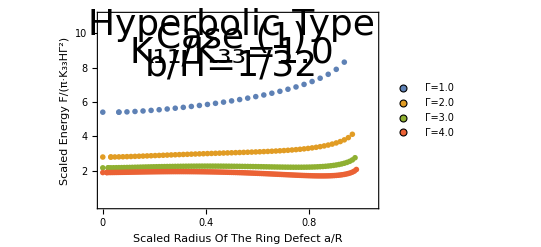

```mathematica
ListPlot[{a,b,e,g},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{2,4,6,8,10},None},{{0,0.2, 0.4, 0.6, 0.8,1},None}}, PlotRange->{{0,1.05},{0,11}},FrameLabel->{{"Scaled Energy F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"Γ=1.0","Γ=2.0","Γ=3.0","Γ=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Hyperbolic Type",Directive[Black,36]],{0.5,10.5}],Text[Style["Case (1)",Directive[Black,36]],{0.5,9.7}],Text[Style["K_11/K_33=1.0",Directive[Black,36]],{0.5,8.9}],Text[Style["b/H=1/32",Directive[Black,36]],{0.5,8.1}]}]
```